Bandstop filter (BSF) 带阻滤波器

## 1. 滤波器设计

滤波器零点和极点(Hz)

```mathematica
fp1 = 30;
fz1 = 80;
fz2 = 207;
fp2 = 550;
```

## 2. 滤波器连续传函

传函系数

```mathematica
Tp1 = 2 Pi fp1;
Tz1 = 2 Pi fz1;
Tz2 = 2 Pi fz2;
Tp2 = 2 Pi fp2;
```

滤波器传函

```mathematica
BSF=TransferFunctionModel[(s/Tz1+1)(s/Tz2+1)/((s/Tp1+1)(s/Tp2+1)),s];
N[BSF,10]
```

(1. (1.+0.0007688644594 s) (1.+0.001989436789 s))/((1.+0.0002893726238 s) (1.+0.00530516477 s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1197.409091034002437236497.40909103400243723641FalseFalseFalseAutomaticNoneAutomatic

bode图如下

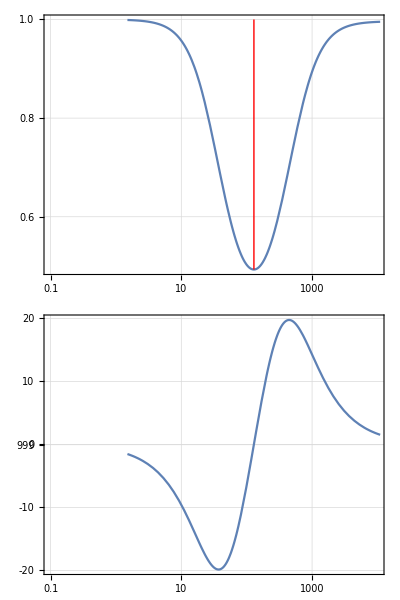

```mathematica
BodePlot[BSF[I 2 Pi f],f,PlotRange->{{{0.1,10000},Automatic},{{0.1,10000},Automatic}},GridLines->Automatic,ImageSize->Medium,StabilityMargins->{True,True},StabilityMarginsStyle->{Red,Red},ScalingFunctions->{{"Log10", "Absolute"}, {"Log10", "Degree"}}]
```

## 3. 滤波器连续传函离散化

采样频率

```mathematica
Fs=10000;
```

采样周期

```mathematica
Ts=1/Fs;
```

传函离散化

```mathematica
BSFz=ToDiscreteTimeModel[BSF,Ts,z,Method->{"BilinearTransform"}];
N[BSFz,10]
```

(0.15942029 (-121.8584073+128.1415927 z) (-9349.690321+10650.30968 z))/((-165.4424808+234.5575192 z) (-990.575222+1009.424778 z))0.0001TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z113.25696945235948834421538202996e102.043008111025497234098739636975e111FalseFalseFalseAutomaticNoneAutomatic

伯德图

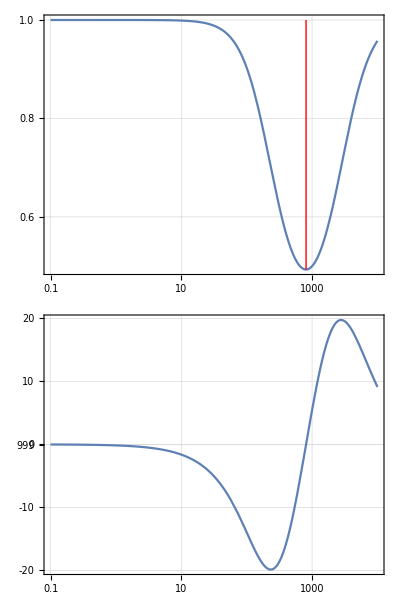

```mathematica
BodePlot[BSFz,{0.1,10000},GridLines->Automatic,ImageSize->Medium,StabilityMargins->{True,True},StabilityMarginsStyle->{Red,Red},ScalingFunctions->{{"Log10", "Absolute"}, {"Log10", "Degree"}}]
```

传函化简

```mathematica
N[TransferFunctionCancel[TransferFunctionExpand[BSFz]],10]
```

(0.918909258 (-0.9509668549+z) (-0.8778796676+z))/((-0.9813264383+z) (-0.7053386367+z))0.0001TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.5012224090144152626303407e71.63370038491545509776405834e71FalseFalseFalseAutomaticNoneAutomatic